# Matrix Element using BSpline

```mathematica
Remove["Global`*"]
$PreRead=(#/.
s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`100."&);
```

Remove::rmnsm: There are no symbols matching "Global`*".

## Test of different Implementation

#### Using BSplineFunction

```mathematica
ai := {0,3,1,5}
pts := Map[{#1, ai[[#1]]}&, {1,2,3,4}]
ϕ[r_] := BSplineFunction[pts][r]
```

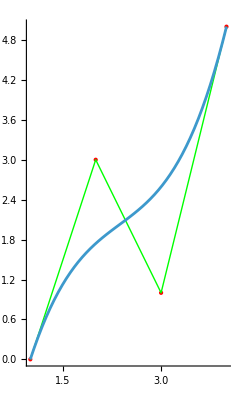

```mathematica
Show[Graphics[{Red,Point[pts],Green,Line[pts]},Axes->True],ParametricPlot[ϕ[r], {r,0,1}]]
```

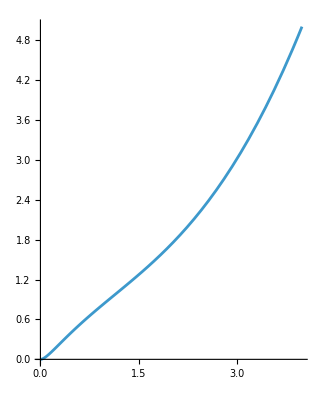

```mathematica
ParametricPlot[ϕ[r], {r,0,1}]
```

#### Using BSplineBasis

```mathematica
(*knot:={0,0,0,0,1/4,1/2,3/4,7/8,8/9,9/10,1,1,1,1}*)
knot := Flatten[{0,0,0,0,0,Table[a,{a,1,9}],10,10,10,10,10}]
ϕi[r_, ai_] := BSplineBasis[{4,knot},ai, r]
```

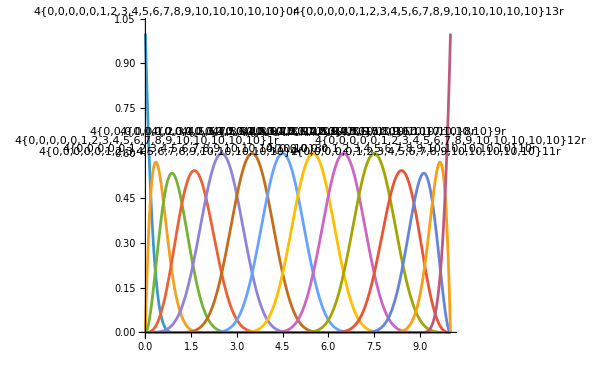

```mathematica
Plot[Evaluate[Table[ϕi[r,i], {i,0,13}]], {r,0,10}, PlotRange->All, PlotLabels->Placed["Expressions",Above]]
```

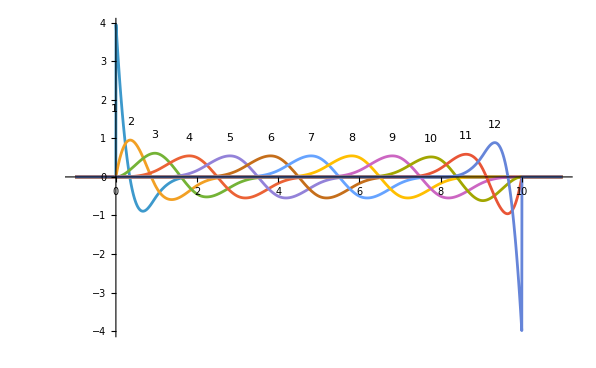

```mathematica
Plot[Evaluate[Table[D[ϕi[x,i],x], {i,1,12}]], {x,-1,11}, PlotRange->All, PlotLabels->Placed[Table[i,{i,1,12}],Above], WorkingPrecision->100]
```

```mathematica
A = Evaluate[Table[Integrate[ϕi[r,ai] ϕi[r,aj],{r,0,10}], {ai,1,12}, {aj,1,12}]];

MatrixForm[A]
```

(209/1260 | 11161/90720 | 106/2835 | 491/120960 | 1/120960 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11161/90720 | 703/3024 | 23791/136080 | 18317/362880 | 667/362880 | 1/272160 | 0 | 0 | 0 | 0 | 0 | 0
106/2835 | 23791/136080 | 5351/17010 | 11933/51840 | 2063/51840 | 43/31104 | 1/362880 | 0 | 0 | 0 | 0 | 0
491/120960 | 18317/362880 | 11933/51840 | 15619/36288 | 44117/181440 | 913/22680 | 251/181440 | 1/362880 | 0 | 0 | 0 | 0
1/120960 | 667/362880 | 2063/51840 | 44117/181440 | 15619/36288 | 44117/181440 | 913/22680 | 251/181440 | 1/362880 | 0 | 0 | 0
0 | 1/272160 | 43/31104 | 913/22680 | 44117/181440 | 15619/36288 | 44117/181440 | 913/22680 | 251/181440 | 1/362880 | 0 | 0
0 | 0 | 1/362880 | 251/181440 | 913/22680 | 44117/181440 | 15619/36288 | 44117/181440 | 913/22680 | 43/31104 | 1/272160 | 0
0 | 0 | 0 | 1/362880 | 251/181440 | 913/22680 | 44117/181440 | 15619/36288 | 44117/181440 | 2063/51840 | 667/362880 | 1/120960
0 | 0 | 0 | 0 | 1/362880 | 251/181440 | 913/22680 | 44117/181440 | 15619/36288 | 11933/51840 | 18317/362880 | 491/120960
0 | 0 | 0 | 0 | 0 | 1/362880 | 43/31104 | 2063/51840 | 11933/51840 | 5351/17010 | 23791/136080 | 106/2835
0 | 0 | 0 | 0 | 0 | 0 | 1/272160 | 667/362880 | 18317/362880 | 23791/136080 | 703/3024 | 11161/90720
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/120960 | 491/120960 | 106/2835 | 11161/90720 | 209/1260)

```mathematica
Integrate[ϕi[r,b] ϕi[r,c]r^2,{r,0,1}, Assumptions->{b,c}∈PositiveReals]
```

Integrate[r^2 BSplineBasis[{3,{0,0,0,1,2,3,4,5,6,7,8,9,10,10,10}},b,r] BSplineBasis[{3,{0,0,0,1,2,3,4,5,6,7,8,9,10,10,10}},c,r],{r,0,1},Assumptions→(b|c)∈ℝ&&b>0&&c>0]

```mathematica
ϕi[r,2]  // PiecewiseExpand
```

Piecewise[{{r^3/6, 0≤r<1}, {1/6 (4-12 r+12 r^2-3 r^3), 1≤r<2}, {1/6 (64-48 r+12 r^2-r^3), 3≤r≤4}, {1/6 (-44+60 r-24 r^2+3 r^3), 2≤r<3}, {0, True}}]

#### Compare Mathematica’s Bsplines with Polynomal Derivation

```mathematica
PiecewiseExpand[BSplineBasis[{2,knot},3, r]]
f := Piecewise[{
{x^2/2-x+1/2, 1≤x≤2},
{-x^2+5x-11/2,  2≤x≤3},
{x^2/2-4x+8,  3≤x≤4}}]
f2 := Piecewise[{
{(x^2-2x+1)/6, 1≤x≤2},
{1/3(-x^2)+2x-14/6,  2≤x≤3},
{(-x^2-10x-25)/6,  3≤x≤4}}]
```

Piecewise[{{1/2 (-11+10 r-2 r^2), 2≤r<3}, {1/2 (16-8 r+r^2), 3≤r≤4}, {1/2 (1-2 r+r^2), 1≤r<2}, {0, True}}]

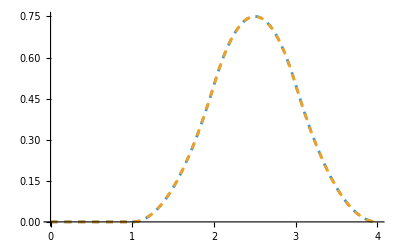

```mathematica
Plot[{f, BSplineBasis[{2,knot},3, x]}, {x,0,4}, PlotRange->All, PlotStyle->Dashed]
```

#### Compare Mathematica with my implementation

```mathematica
Clear[bspline];

knot := Flatten[{0,0,0,Table[a,{a,1,9}],10,10,10}]

(*Zeroth–degree basis functions*)
bspline[i_,1,t_,knots_]:=If[knots[[i]]<=t<knots[[i+1]],1,0];

(*Higher–degree basis functions via recursion*)
bspline[i_,k_,t_,knots_]:=Module[{denom1,denom2,term1,term2},denom1=knots[[i+k-1]]-knots[[i]];
denom2=knots[[i+k]]-knots[[i+1]];
term1=If[denom1==0,0,(t-knots[[i]])/denom1*bspline[i,k-1,t,knots]];
term2=If[denom2==0,0,(knots[[i+k]]-t)/denom2*bspline[i+1,k-1,t,knots]];
term1+term2];
```

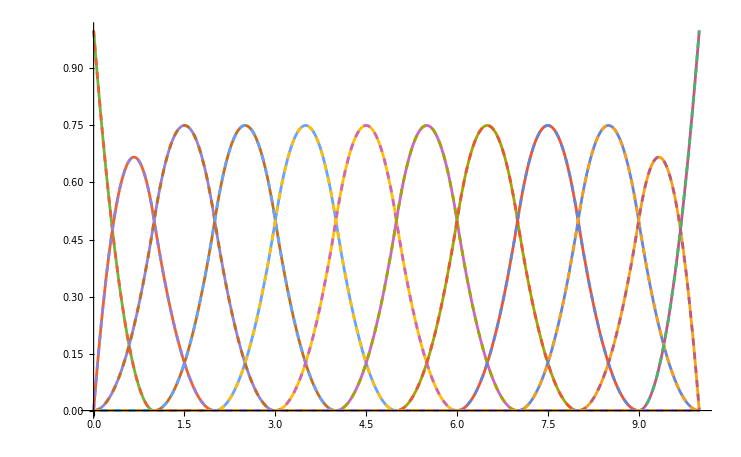

```mathematica
ps=Join[Table[Normal,16], Table[Dashed,16]];
Plot[{
Evaluate[Table[bspline[i,3,r,knot], {i,1,16}]],
Evaluate[Table[BSplineBasis[{2, knot},i, r], {i,0,15}]]
},
{r,0,10}, PlotRange->All, PlotStyle->ps
]
```

Warning : Not the same notation used in Physics (cf. Johnson definition) and Mathematica’s implementation, when using BSplineBasis:

## Overlaps Matrix S

```mathematica
ClearAll["`*"]
```

```mathematica
order = 3;
(*knot := Flatten[{0,0,0,Table[a,{a,1,9}],10,10,10}]*)
knot := Flatten[{0,0,0,3,5,8,9,10,10,10}]
n = Length[knot]-order-2
ϕi[r_, i_] := BSplineBasis[{order,knot},i, r]
```

5

```mathematica
S =  Evaluate[Table[Integrate[ϕi[r,ai] ϕi[r,aj],{r,0,10}], {ai,1,n-1}, {aj,1,n-1}]];
S // MatrixForm
```

(3888/4375 | 1960547/3360000 | 232171/3360000 | 243/112000
1960547/3360000 | 16701/16000 | 21331/44800 | 647/10500
232171/3360000 | 21331/44800 | 3189/4000 | 129557/336000
243/112000 | 647/10500 | 129557/336000 | 137/224)

## Matrix Sigma P

```mathematica
spSL[k_,f_]:=-c(D[f, r]+k/r f) (* check form *)
spLS[k_,f_]:=c(D[f, r]-k/r f) 
sigmapSL = Evaluate[Table[Integrate[ϕi[r,ai] spSL[k, ϕi[r,aj]], {r,0,Infinity}], {ai,1,n-1}, {aj,1,n-1}]];
sigmapLS = Evaluate[Table[Integrate[ϕi[r,ai] spLS[k, ϕi[r,aj]], {r,0,Infinity}], {ai,1,n-1}, {aj,1,n-1}]];
sigmapSL // MatrixForm
sigmapLS // MatrixForm
```

((125769 c k-64800 c k Log[5/3]+204800 c k Log[5]-204800 c k Log[8])/11250 | (-141981 c-8593673 c k+1555200 c k Log[5/3]-16435200 c k Log[5]+16435200 c k Log[8])/480000 | (-126639 c+20532333 c k-3110400 c k ArcCoth[4]+42035200 c k Log[5]-42035200 c k Log[8])/1440000 | -(c (729+601653 k+1280000 k Log[5]-1280000 k Log[8]))/144000
(141981 c-8593673 c k+1555200 c k Log[5/3]-16435200 c k Log[5]+16435200 c k Log[8])/480000 | -(3 (-744829 c k+9841500 c k ArcCoth[17]+343470 c k Log[8/5]+9720 c k Log[5/3]))/16000 | (-89169 c-123588805 c k+349920 c k ArcCoth[4]+1970487000 c k ArcCoth[17]+15812460 c k Log[8/5])/288000 | (-6897 c+54981346 c k-924007500 c k ArcCoth[17]+1203750 c k Log[5]-1203750 c k Log[8])/72000
(126639 c+20532333 c k-3110400 c k ArcCoth[4]+42035200 c k Log[5]-42035200 c k Log[8])/1440000 | (89169 c-123588805 c k+349920 c k ArcCoth[4]+1970487000 c k ArcCoth[17]+15812460 c k Log[8/5])/288000 | (185011274 c k-29160 c k ArcCoth[4]-1440000000 c k ArcCoth[19]-913276125 c k Log[9/8]-3370205 c k Log[8/5])/72000 | (-47127 c-1466536589 c k+20160000000 c k ArcCoth[19]+3426052500 c k Log[9/8]-2052500 c k Log[5]+2052500 c k Log[8])/144000
-(c (-729+601653 k+1280000 k Log[5]-1280000 k Log[8]))/144000 | (6897 c+54981346 c k-924007500 c k ArcCoth[17]-1203750 c k Log[8/5])/72000 | (47127 c-1466536589 c k+20160000000 c k ArcCoth[19]+3426052500 c k Log[9/8]-2052500 c k Log[5]+2052500 c k Log[8])/144000 | (81914217 c k-64262250 c k Log[9/8]+6250 c k Log[5]-6250 c k Log[8]+705600000 c k Log[9]-705600000 c k Log[10])/1440)

((125769 c k-64800 c k Log[5/3]+204800 c k Log[5]-204800 c k Log[8])/11250 | (141981 c-8593673 c k+1555200 c k Log[5/3]-16435200 c k Log[5]+16435200 c k Log[8])/480000 | (126639 c+20532333 c k-3110400 c k ArcCoth[4]+42035200 c k Log[5]-42035200 c k Log[8])/1440000 | -(c (-729+601653 k+1280000 k Log[5]-1280000 k Log[8]))/144000
(-141981 c-8593673 c k+1555200 c k Log[5/3]-16435200 c k Log[5]+16435200 c k Log[8])/480000 | -(3 (-744829 c k+9841500 c k ArcCoth[17]+343470 c k Log[8/5]+9720 c k Log[5/3]))/16000 | (89169 c-123588805 c k+349920 c k ArcCoth[4]+1970487000 c k ArcCoth[17]+15812460 c k Log[8/5])/288000 | (6897 c+54981346 c k-924007500 c k ArcCoth[17]-1203750 c k Log[8/5])/72000
(-126639 c+20532333 c k-3110400 c k ArcCoth[4]+42035200 c k Log[5]-42035200 c k Log[8])/1440000 | (-89169 c-123588805 c k+349920 c k ArcCoth[4]+1970487000 c k ArcCoth[17]+15812460 c k Log[8/5])/288000 | (185011274 c k-29160 c k ArcCoth[4]-1440000000 c k ArcCoth[19]-913276125 c k Log[9/8]-3370205 c k Log[8/5])/72000 | (47127 c-1466536589 c k+20160000000 c k ArcCoth[19]+3426052500 c k Log[9/8]-2052500 c k Log[5]+2052500 c k Log[8])/144000
-(c (729+601653 k+1280000 k Log[5]-1280000 k Log[8]))/144000 | (-6897 c+54981346 c k-924007500 c k ArcCoth[17]+1203750 c k Log[5]-1203750 c k Log[8])/72000 | (-47127 c-1466536589 c k+20160000000 c k ArcCoth[19]+3426052500 c k Log[9/8]-2052500 c k Log[5]+2052500 c k Log[8])/144000 | (81914217 c k-64262250 c k Log[9/8]+6250 c k Log[5]-6250 c k Log[8]+705600000 c k Log[9]-705600000 c k Log[10])/1440)

## Matrix V

```mathematica
v=-Z/r; (* check form *)
V = Evaluate[Table[Integrate[ϕi[r,ai] v ϕi[r,aj], {r,0,Infinity}], {ai,1,n-1}, {aj,1,n-1}]];
V // MatrixForm
```

((125769 Z-129600 Z ArcCoth[4]+204800 Z Log[5]-204800 Z Log[8])/11250 | (-8593673 Z+16435200 Z Log[8/5]+1555200 Z Log[5/3])/480000 | (20532333 Z-42035200 Z Log[8/5]-1555200 Z Log[5/3])/1440000 | (Z (-601653+1280000 Log[8/5]))/144000
(-8593673 Z+16435200 Z Log[8/5]+1555200 Z Log[5/3])/480000 | -(3 (-744829 Z+19440 Z ArcCoth[4]+9841500 Z ArcCoth[17]-343470 Z Log[5]+343470 Z Log[8]))/16000 | (-24717761 Z+197048700 Z Log[9/8]+3162492 Z Log[8/5]+34992 Z Log[5/3])/57600 | (27490673 Z-231001875 Z Log[9/8]-601875 Z Log[8/5])/36000
(20532333 Z-42035200 Z Log[8/5]-1555200 Z Log[5/3])/1440000 | (-24717761 Z+197048700 Z Log[9/8]+3162492 Z Log[8/5]+34992 Z Log[5/3])/57600 | (185011274 Z-29160 Z ArcCoth[4]-1826552250 Z ArcCoth[17]-1440000000 Z ArcCoth[19]+3370205 Z Log[5]-3370205 Z Log[8])/72000 | (-1466536589 Z+20160000000 Z ArcCoth[19]+3426052500 Z Log[9/8]+2052500 Z Log[8/5])/144000
(Z (-601653+1280000 Log[8/5]))/144000 | (27490673 Z-231001875 Z Log[9/8]-601875 Z Log[8/5])/36000 | (-1466536589 Z+20160000000 Z ArcCoth[19]+3426052500 Z Log[9/8]+2052500 Z Log[8/5])/144000 | (81914217 Z-128524500 Z ArcCoth[17]-1411200000 Z ArcCoth[19]+6250 Z Log[5]-6250 Z Log[8])/1440)

## Matrix DD

```mathematica
DD = ArrayFlatten[{{V, sigmapLS}, {sigmapSL, V - 2 c^2 S}} ] ;(*Check tranposed and sign*)
{DD // Dimensions, SymmetricMatrixQ[DD]}
DD // MatrixForm
```

{{8,8},True}

((125769 Z-129600 Z ArcCoth[4]+204800 Z Log[5]-204800 Z Log[8])/11250 | (-8593673 Z+16435200 Z Log[8/5]+1555200 Z Log[5/3])/480000 | (20532333 Z-42035200 Z Log[8/5]-1555200 Z Log[5/3])/1440000 | (Z (-601653+1280000 Log[8/5]))/144000 | (125769 c k-64800 c k Log[5/3]+204800 c k Log[5]-204800 c k Log[8])/11250 | (141981 c-8593673 c k+1555200 c k Log[5/3]-16435200 c k Log[5]+16435200 c k Log[8])/480000 | (126639 c+20532333 c k-3110400 c k ArcCoth[4]+42035200 c k Log[5]-42035200 c k Log[8])/1440000 | -(c (-729+601653 k+1280000 k Log[5]-1280000 k Log[8]))/144000
(-8593673 Z+16435200 Z Log[8/5]+1555200 Z Log[5/3])/480000 | -(3 (-744829 Z+19440 Z ArcCoth[4]+9841500 Z ArcCoth[17]-343470 Z Log[5]+343470 Z Log[8]))/16000 | (-24717761 Z+197048700 Z Log[9/8]+3162492 Z Log[8/5]+34992 Z Log[5/3])/57600 | (27490673 Z-231001875 Z Log[9/8]-601875 Z Log[8/5])/36000 | (-141981 c-8593673 c k+1555200 c k Log[5/3]-16435200 c k Log[5]+16435200 c k Log[8])/480000 | -(3 (-744829 c k+9841500 c k ArcCoth[17]+343470 c k Log[8/5]+9720 c k Log[5/3]))/16000 | (89169 c-123588805 c k+349920 c k ArcCoth[4]+1970487000 c k ArcCoth[17]+15812460 c k Log[8/5])/288000 | (6897 c+54981346 c k-924007500 c k ArcCoth[17]-1203750 c k Log[8/5])/72000
(20532333 Z-42035200 Z Log[8/5]-1555200 Z Log[5/3])/1440000 | (-24717761 Z+197048700 Z Log[9/8]+3162492 Z Log[8/5]+34992 Z Log[5/3])/57600 | (185011274 Z-29160 Z ArcCoth[4]-1826552250 Z ArcCoth[17]-1440000000 Z ArcCoth[19]+3370205 Z Log[5]-3370205 Z Log[8])/72000 | (-1466536589 Z+20160000000 Z ArcCoth[19]+3426052500 Z Log[9/8]+2052500 Z Log[8/5])/144000 | (-126639 c+20532333 c k-3110400 c k ArcCoth[4]+42035200 c k Log[5]-42035200 c k Log[8])/1440000 | (-89169 c-123588805 c k+349920 c k ArcCoth[4]+1970487000 c k ArcCoth[17]+15812460 c k Log[8/5])/288000 | (185011274 c k-29160 c k ArcCoth[4]-1440000000 c k ArcCoth[19]-913276125 c k Log[9/8]-3370205 c k Log[8/5])/72000 | (47127 c-1466536589 c k+20160000000 c k ArcCoth[19]+3426052500 c k Log[9/8]-2052500 c k Log[5]+2052500 c k Log[8])/144000
(Z (-601653+1280000 Log[8/5]))/144000 | (27490673 Z-231001875 Z Log[9/8]-601875 Z Log[8/5])/36000 | (-1466536589 Z+20160000000 Z ArcCoth[19]+3426052500 Z Log[9/8]+2052500 Z Log[8/5])/144000 | (81914217 Z-128524500 Z ArcCoth[17]-1411200000 Z ArcCoth[19]+6250 Z Log[5]-6250 Z Log[8])/1440 | -(c (729+601653 k+1280000 k Log[5]-1280000 k Log[8]))/144000 | (-6897 c+54981346 c k-924007500 c k ArcCoth[17]+1203750 c k Log[5]-1203750 c k Log[8])/72000 | (-47127 c-1466536589 c k+20160000000 c k ArcCoth[19]+3426052500 c k Log[9/8]-2052500 c k Log[5]+2052500 c k Log[8])/144000 | (81914217 c k-64262250 c k Log[9/8]+6250 c k Log[5]-6250 c k Log[8]+705600000 c k Log[9]-705600000 c k Log[10])/1440
(125769 c k-64800 c k Log[5/3]+204800 c k Log[5]-204800 c k Log[8])/11250 | (-141981 c-8593673 c k+1555200 c k Log[5/3]-16435200 c k Log[5]+16435200 c k Log[8])/480000 | (-126639 c+20532333 c k-3110400 c k ArcCoth[4]+42035200 c k Log[5]-42035200 c k Log[8])/1440000 | -(c (729+601653 k+1280000 k Log[5]-1280000 k Log[8]))/144000 | -(7776 c^2)/4375+(125769 Z-129600 Z ArcCoth[4]+204800 Z Log[5]-204800 Z Log[8])/11250 | -(1960547 c^2)/1680000+(-8593673 Z+16435200 Z Log[8/5]+1555200 Z Log[5/3])/480000 | -(232171 c^2)/1680000+(20532333 Z-42035200 Z Log[8/5]-1555200 Z Log[5/3])/1440000 | -(243 c^2)/56000+(Z (-601653+1280000 Log[8/5]))/144000
(141981 c-8593673 c k+1555200 c k Log[5/3]-16435200 c k Log[5]+16435200 c k Log[8])/480000 | -(3 (-744829 c k+9841500 c k ArcCoth[17]+343470 c k Log[8/5]+9720 c k Log[5/3]))/16000 | (-89169 c-123588805 c k+349920 c k ArcCoth[4]+1970487000 c k ArcCoth[17]+15812460 c k Log[8/5])/288000 | (-6897 c+54981346 c k-924007500 c k ArcCoth[17]+1203750 c k Log[5]-1203750 c k Log[8])/72000 | -(1960547 c^2)/1680000+(-8593673 Z+16435200 Z Log[8/5]+1555200 Z Log[5/3])/480000 | -(16701 c^2)/8000-(3 (-744829 Z+19440 Z ArcCoth[4]+9841500 Z ArcCoth[17]-343470 Z Log[5]+343470 Z Log[8]))/16000 | -(21331 c^2)/22400+(-24717761 Z+197048700 Z Log[9/8]+3162492 Z Log[8/5]+34992 Z Log[5/3])/57600 | -(647 c^2)/5250+(27490673 Z-231001875 Z Log[9/8]-601875 Z Log[8/5])/36000
(126639 c+20532333 c k-3110400 c k ArcCoth[4]+42035200 c k Log[5]-42035200 c k Log[8])/1440000 | (89169 c-123588805 c k+349920 c k ArcCoth[4]+1970487000 c k ArcCoth[17]+15812460 c k Log[8/5])/288000 | (185011274 c k-29160 c k ArcCoth[4]-1440000000 c k ArcCoth[19]-913276125 c k Log[9/8]-3370205 c k Log[8/5])/72000 | (-47127 c-1466536589 c k+20160000000 c k ArcCoth[19]+3426052500 c k Log[9/8]-2052500 c k Log[5]+2052500 c k Log[8])/144000 | -(232171 c^2)/1680000+(20532333 Z-42035200 Z Log[8/5]-1555200 Z Log[5/3])/1440000 | -(21331 c^2)/22400+(-24717761 Z+197048700 Z Log[9/8]+3162492 Z Log[8/5]+34992 Z Log[5/3])/57600 | -(3189 c^2)/2000+(185011274 Z-29160 Z ArcCoth[4]-1826552250 Z ArcCoth[17]-1440000000 Z ArcCoth[19]+3370205 Z Log[5]-3370205 Z Log[8])/72000 | -(129557 c^2)/168000+(-1466536589 Z+20160000000 Z ArcCoth[19]+3426052500 Z Log[9/8]+2052500 Z Log[8/5])/144000
-(c (-729+601653 k+1280000 k Log[5]-1280000 k Log[8]))/144000 | (6897 c+54981346 c k-924007500 c k ArcCoth[17]-1203750 c k Log[8/5])/72000 | (47127 c-1466536589 c k+20160000000 c k ArcCoth[19]+3426052500 c k Log[9/8]-2052500 c k Log[5]+2052500 c k Log[8])/144000 | (81914217 c k-64262250 c k Log[9/8]+6250 c k Log[5]-6250 c k Log[8]+705600000 c k Log[9]-705600000 c k Log[10])/1440 | -(243 c^2)/56000+(Z (-601653+1280000 Log[8/5]))/144000 | -(647 c^2)/5250+(27490673 Z-231001875 Z Log[9/8]-601875 Z Log[8/5])/36000 | -(129557 c^2)/168000+(-1466536589 Z+20160000000 Z ArcCoth[19]+3426052500 Z Log[9/8]+2052500 Z Log[8/5])/144000 | -(137 c^2)/112+(81914217 Z-128524500 Z ArcCoth[17]-1411200000 Z ArcCoth[19]+6250 Z Log[5]-6250 Z Log[8])/1440)

```mathematica
CC = ArrayFlatten[{{S,0},{0,S}}];
{CC // Dimensions, SymmetricMatrixQ[CC]}
CC // MatrixForm
```

{{8,8},True}

(3888/4375 | 1960547/3360000 | 232171/3360000 | 243/112000 | 0 | 0 | 0 | 0
1960547/3360000 | 16701/16000 | 21331/44800 | 647/10500 | 0 | 0 | 0 | 0
232171/3360000 | 21331/44800 | 3189/4000 | 129557/336000 | 0 | 0 | 0 | 0
243/112000 | 647/10500 | 129557/336000 | 137/224 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3888/4375 | 1960547/3360000 | 232171/3360000 | 243/112000
0 | 0 | 0 | 0 | 1960547/3360000 | 16701/16000 | 21331/44800 | 647/10500
0 | 0 | 0 | 0 | 232171/3360000 | 21331/44800 | 3189/4000 | 129557/336000
0 | 0 | 0 | 0 | 243/112000 | 647/10500 | 129557/336000 | 137/224)

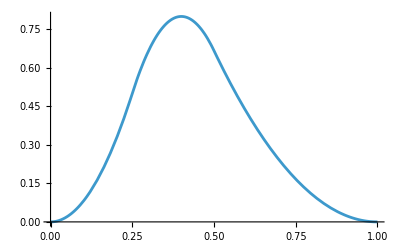

```mathematica
Plot[BSplineBasis[{2, {0.0,0.25, 0.5,1.0}}, 0, r], {r,0,1}]
```

```mathematica
BSplineBasis[{3, {0.0,0.25,0.5,0.6,0.7,1.0}}, 0, r] // PiecewiseExpand
```

Piecewise[{{13.3333 r^3, 0.≤r<0.25}, {38.1111-163.333 r+233.333 r^2-111.111 r^3, 0.6≤r≤0.7}, {1.11111-13.3333 r+53.3333 r^2-57.7778 r^3, 0.25≤r<0.5}, {-33.8889+196.667 r-366.667 r^2+222.222 r^3, 0.5≤r<0.6}, {0, True}}]

```mathematica
BSplineBasis[{5,{0.0,0.0,0.0,0.0,0.5,1.0,1.0}}, 0, r] // PiecewiseExpand
```

Piecewise[{{20. r^2-80. r^3+110. r^4-52. r^5, 0.≤r<0.5}, {-2.+20. r-60. r^2+80. r^3-50. r^4+12. r^5, 0.5≤r≤1.}, {0, True}}]